```mathematica
(* Assuming all output files are in the same directory as the notebook *)
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* helper function to input four-color screen or equatorial passings information *)
ReadinFile[filename_]:=Module[{str,temptab,xpos,ypos,throw,color},
str=OpenRead[filename];
temptab={};
ReadLine[str]; (* read first line *)
xpos=Read[str,Real];
While[!(xpos=== EndOfFile),
ypos=Read[str,Real];
color=Read[str,Real]; (* color or equatorial passes *)
temptab=Join[temptab,{{xpos,ypos,color}}];
xpos=Read[str,Real];
];
Close[str];
temptab
];
```

```mathematica
(***** SIMPLESQUAREMESH illustration *****)
```

```mathematica
(*** read in data: four color screen of Kerr (a=0.5) at 90 degree inclination ***)
Timing[filedataSimple=ReadinFile["sampleoutput_simplemesh_221202-125440_FourColorScreen.dat"];]
```

{0.59375,Null}

```mathematica
(*** max row/column ***)
maxnr=Round[Max[filedataSimple[[All,1]]]]
```

99

```mathematica
(*** File data consists of triplets {x, y, color} - convert this to table with entries (x,y) = color ***)
Timing[SimpleArray=ConstantArray[-1,{maxnr+1,maxnr+1}];
For[i=1,i≤Length[filedataSimple],i=i+1,
SimpleArray[[ Round[filedataSimple[[i,2]]]+1, Round[filedataSimple[[i,1]]]+1 ]]=Round[filedataSimple[[i,3]]];
];]
```

{0.03125,Null}

```mathematica
(*** plot this ***)
Timing[plotSimple=ArrayPlot[SimpleArray,ColorRules->{1->Red,0->Black,2->Blue,3->Green,4->Yellow,-1->White},AspectRatio->1];]
```

{0.03125,Null}

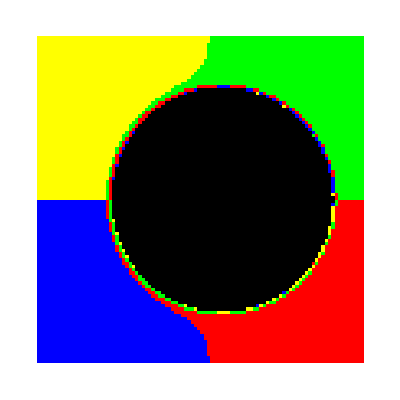

```mathematica
plotSimple
```

```mathematica
(***** ADAPTIVE SQUARE MESH illustration *****)
```

```mathematica
(*** read in file: four color screen of Kerr (a=0.5) at 90 degree inclination ***)
Timing[filedataAdaptive=ReadinFile["sampleoutput_adaptivemesh_221202-125808_FourColorScreen.dat"];]
```

{4.01563,Null}

```mathematica
(*** note much larger row/columns ***)
maxnr=Round[Max[filedataAdaptive[[All,1]]]]
```

792

```mathematica
(*** convert from triplets to array as before ***)
Timing[AdaptiveArray=ConstantArray[-1,{maxnr+1,maxnr+1}];
For[i=1,i≤Length[filedataAdaptive],i=i+1,
AdaptiveArray[[ Round[filedataAdaptive[[i,2]]]+1, Round[filedataAdaptive[[i,1]]]+1 ]]=Round[filedataAdaptive[[i,3]]];
];]
```

{0.09375,Null}

```mathematica
Timing[plotAdaptive=ArrayPlot[AdaptiveArray,ColorRules->{1->Red,0->Black,2->Blue,3->Green,4->Yellow,-1->White},AspectRatio->1];]
```

{0.765625,Null}

```mathematica
(* there is a lot of white space since the adaptive mesh did not refine everywhere! *)
plotAdaptive
```

-Graphics-

```mathematica
(* if we want to fill in the colors, we can do a simple interpolation on the data *)
Timing[funcinterpol=Interpolation[{{#[[1]],#[[2]]},#[[3]]}&/@filedataAdaptive,InterpolationOrder->1];]
Timing[AdaptiveArrayInterpol=Table[Round[funcinterpol[jj,ii]],{ii,0,maxnr,1},{jj,0,maxnr,1}];]
```

{0.15625,Null}

{1.0625,Null}

```mathematica
(* plot the fully interpolated data *)
Timing[plotAdaptiveInterpol=ArrayPlot[AdaptiveArrayInterpol,ColorRules->{1->Red,0->Black,2->Blue,3->Green,4->Yellow,-1->White},AspectRatio->1];]
```

{0.515625,Null}

```mathematica
(* this looks much nicer! *)
plotAdaptiveInterpol
```

-Graphics-

```mathematica
(***** ADAPTIVE SQUARE MESH & photon rings *****)
```

```mathematica
(* read in file: four color screen of Kerr (a=0.5) at 17 degree inclination *)
Timing[filedataColor=ReadinFile["sampleoutput_adaptivemesh_rings_221202-140701_FourColorScreen.dat"];]
```

{15.7031,Null}

```mathematica
maxnr=Round[Max[filedataColor[[All,1]]]]
```

1120

```mathematica
(* create interpolated color figure as above *)
Timing[funcinterpol=Interpolation[{{#[[1]],#[[2]]},#[[3]]}&/@filedataColor,InterpolationOrder->1];]
Timing[AdaptiveArrayInterpol=Table[Round[funcinterpol[jj,ii]],{ii,0,maxnr,1},{jj,0,maxnr,1}];]
Timing[plotAdaptiveInterpol=ArrayPlot[AdaptiveArrayInterpol,ColorRules->{1->Red,0->Black,2->Blue,3->Green,4->Yellow,-1->White},AspectRatio->1];]
plotAdaptiveInterpol
```

{0.390625,Null}

{2.17188,Null}

{0.90625,Null}

-Graphics-

```mathematica
(* read in file of equatorial passes (same Kerr (a=0.5) at 17 degree inclination) *) 
Timing[filedataPasses=ReadinFile["sampleoutput_adaptivemesh_rings_221202-140701_EquatPasses.dat"];]
```

{16.1875,Null}

```mathematica
Timing[funcinterpol=Interpolation[{{#[[1]],#[[2]]},#[[3]]}&/@filedataPasses,InterpolationOrder->1];]
Timing[AdaptiveArrayInterpol=Table[Round[funcinterpol[jj,ii]],{ii,0,maxnr,1},{jj,0,maxnr,1}];]
Timing[plotAdaptiveInterpol=ArrayPlot[AdaptiveArrayInterpol,ColorFunction->"Rainbow",AspectRatio->1];]
```

{0.34375,Null}

{2.07813,Null}

{1.34375,Null}

```mathematica
(* all rings together; note that geodesics that fall into the horizon are assigned a negative number *)
plotAdaptiveInterpol
```

-Graphics-

```mathematica
(* we can extract the ≥2 photon rings; note the Abs[.] needed because geodesics falling into the horizon get assigned a negative number *)
Timing[ArraynGeq2=Table[If[Abs[AdaptiveArrayInterpol[[ii,jj]]]≥ 2,1,0],{ii,1,maxnr+1,1},{jj,1,maxnr+1,1}];]
```

{1.,Null}

```mathematica
Timing[plotnGeq2=ArrayPlot[ArraynGeq2,AspectRatio->1];]
```

{0.03125,Null}

```mathematica
plotnGeq2
```

-Graphics-

```mathematica
(* The n≥3 photon rings *)
Timing[ArraynGeq3=Table[If[Abs[AdaptiveArrayInterpol[[ii,jj]]]≥3,1,0],{ii,1,maxnr+1,1},{jj,1,maxnr+1,1}];]
```

{1.01563,Null}

```mathematica
Timing[plotnGeq3=ArrayPlot[ArraynGeq3,AspectRatio->1];]
```

{0.03125,Null}

```mathematica
plotnGeq3
```

-Graphics-

```mathematica
(* we even have high enough resolution to pick out the n≥4 photon ring, although here we begin to see pixelation *)
Timing[ArraynGeq4=Table[If[Abs[AdaptiveArrayInterpol[[ii,jj]]]≥4,1,0],{ii,1,maxnr+1,1},{jj,1,maxnr+1,1}];]
```

{0.96875,Null}

```mathematica
Timing[plotnGeq4=ArrayPlot[ArraynGeq4,AspectRatio->1];]
```

{0.015625,Null}

```mathematica
plotnGeq4
```

-Graphics-